# Find closest point on the MT

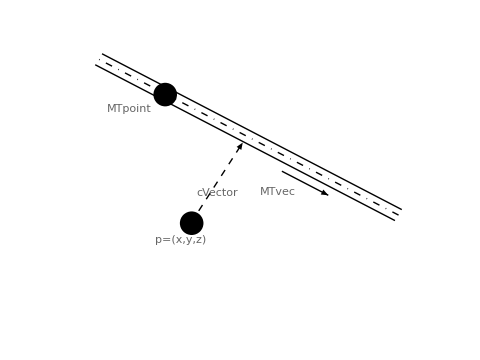

We have the situation shown above, where we want to find the vector cVector from the point (x,y,z) to closest point on the surface of the MT. The MT centerline is defined by a point MTpoint and a unit vector MTvec.

t=((MTpoint-p)·MTvec)MTvec
v=(MTpoint-p)-t
   =(MTpoint-p)- ((MTpoint-p)·MTvec)MTvec
cVector=(1-R_MT)v

## Find the vector from the point to the closest point on the MT

```mathematica
pointToMTvec=(1-RMT[MTnum])*
({MTpoint[MTnum][0],MTpoint[MTnum][1],MTpoint[MTnum][2]}-{x,y,z})-Dot[{MTpoint[MTnum][0],MTpoint[MTnum][1],MTpoint[MTnum][2]}-{x,y,z},{MTvec[MTnum][0],MTvec[MTnum][1],MTvec[MTnum][2]}]*{MTvec[MTnum][0],MTvec[MTnum][1],MTvec[MTnum][2]}
```

{(1-RMT[MTnum]) (-x+MTpoint[MTnum][0])-MTvec[MTnum][0] ((-x+MTpoint[MTnum][0]) MTvec[MTnum][0]+(-y+MTpoint[MTnum][1]) MTvec[MTnum][1]+(-z+MTpoint[MTnum][2]) MTvec[MTnum][2]),(1-RMT[MTnum]) (-y+MTpoint[MTnum][1])-MTvec[MTnum][1] ((-x+MTpoint[MTnum][0]) MTvec[MTnum][0]+(-y+MTpoint[MTnum][1]) MTvec[MTnum][1]+(-z+MTpoint[MTnum][2]) MTvec[MTnum][2]),(1-RMT[MTnum]) (-z+MTpoint[MTnum][2])-MTvec[MTnum][2] ((-x+MTpoint[MTnum][0]) MTvec[MTnum][0]+(-y+MTpoint[MTnum][1]) MTvec[MTnum][1]+(-z+MTpoint[MTnum][2]) MTvec[MTnum][2])}

## The associated distance

```mathematica
dist=Sqrt[Total[{cVector[0],cVector[1],cVector[2]}^2]]
```

√(cVector[0]^2+cVector[1]^2+cVector[2]^2)

## The associated point

```mathematica
closestPoint={x,y,z}+{cVector[0],cVector[1],cVector[2]}
```

{x+cVector[0],y+cVector[1],z+cVector[2]}

## Write to file

```mathematica
DeleteFile[NotebookDirectory[]<>"pointToMT_formulae.txt"]
outfileLoc=CreateFile[NotebookDirectory[]<>"pointToMT_formulae.txt"];
outfile=File[outfileLoc];
```

```mathematica
WriteString[outfile,CForm[cVector[0]==pointToMTvec[[1]]],";","\n"]
WriteString[outfile,CForm[cVector[1]==pointToMTvec[[2]]],";","\n"]
WriteString[outfile,CForm[cVector[2]==pointToMTvec[[3]]],";","\n\n"]

WriteString[outfile,CForm[MTdist ==dist],";","\n\n"];

WriteString[outfile,CForm[cPoint[0]==closestPoint[[1]]],";","\n"]
WriteString[outfile,CForm[cPoint[1]==closestPoint[[2]]],";","\n"]
WriteString[outfile,CForm[cPoint[2]==closestPoint[[3]]],";","\n"]
```

```mathematica
Close[outfile]
```

/Users/Matt/project_code/Motor_Freedom/tools/pointToMT_formulae.txt